## Hexi—PS9—2025-02-21

### Exercises from EIWL3 Section 23

```mathematica
N[Sqrt[2],500]
```

1.4142135623730950488016887242096980785696718753769480731766797379907324784621070388503875343276415727350138462309122970249248360558507372126441214970999358314132226659275055927557999505011527820605714701095599716059702745345968620147285174186408891986095523292304843087143214508397626036279952514079896872533965463318088296406206152583523950547457502877599617298355752203375318570113543746034084988471603868999706990048150305440277903164542478230684929369186215805784631115966687130130156185689872372

```mathematica
Table[RandomReal[1],10]
```

{0.582737,0.346835,0.233306,0.794703,0.125949,0.721753,0.553628,0.956277,0.0217854,0.389199}

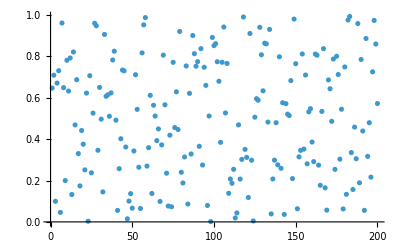

```mathematica
ListPlot[Table[RandomReal[1],200]]
```

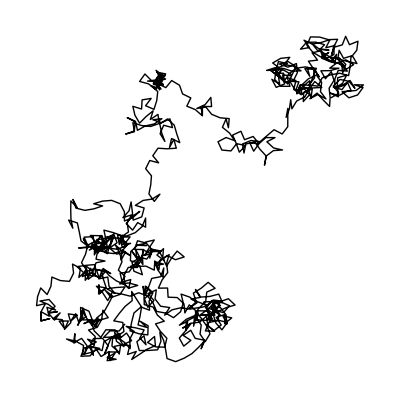

```mathematica
Graphics[Line[AnglePath[RandomReal[{0,2Pi},1000]]]]
```

```mathematica
Table[Mod[n^2,10],{n,0,30}]
```

{0,1,4,9,6,5,6,9,4,1,0,1,4,9,6,5,6,9,4,1,0,1,4,9,6,5,6,9,4,1,0}

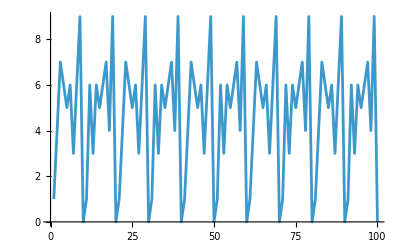

```mathematica
ListLinePlot[Table[Mod[n^n,10],{n,1,100}]]
```

```mathematica
Table[Round[Pi^n],{n,10}]
```

{3,10,31,97,306,961,3020,9489,29809,93648}

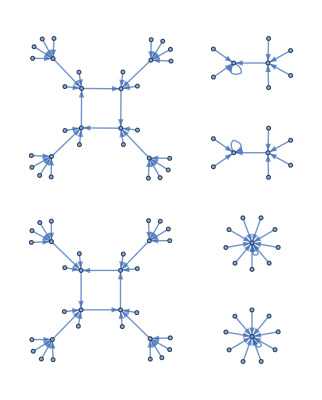

```mathematica
Graph[Flatten[Table[n->Mod[n^2,100],{n,0,99}]]]
```

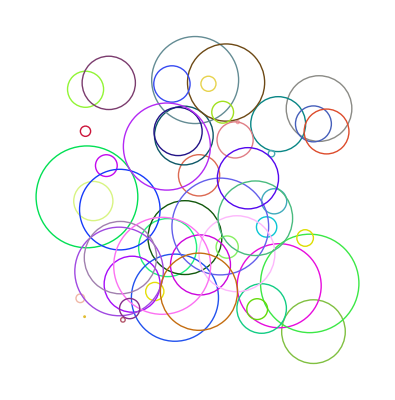

```mathematica
Graphics[Table[Style[Circle[{RandomReal[10],RandomReal[10]},RandomReal[2]],RandomColor[]],50]]
```

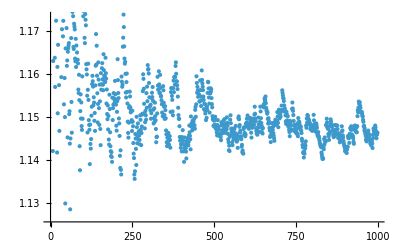

```mathematica
ListPlot[Table[Prime[n]/(n Log[n]),{n,2,1000}]]
```

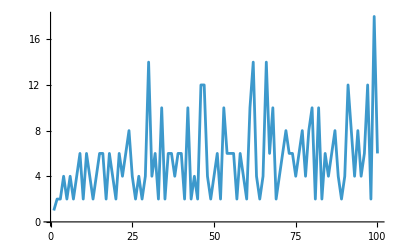

```mathematica
ListLinePlot[Table[Prime[n+1]-Prime[n],{n,100
}]]
```

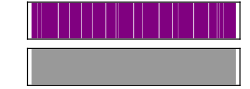

```mathematica
Sound[Table[SoundNote["C",RandomReal[0.5]],20]]
```

```mathematica
ArrayPlot[Table[Mod[i,j],{i,50},{j,50}]]
```

-Graphics-

```mathematica
Table[ArrayPlot[Table[Mod[x^y,n],{x,50},{y,50}]],{n,2,10}]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

### Exercises from EIWL3 Section 24

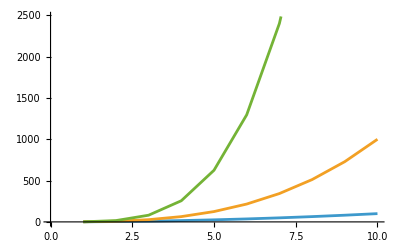

```mathematica
ListLinePlot[{Table[x^2,{x,10}],Table[x^3,{x,10}],Table[x^4,{x,10}]}]
```

```mathematica
ListLinePlot[Table[Prime[x],{x,20}],Filling->Axis,Mesh->All,MeshStyle->Red]
```

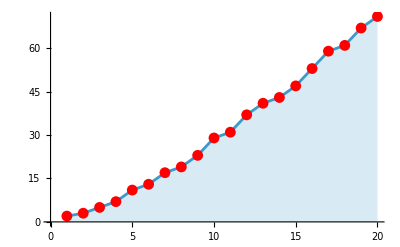

```mathematica
ListPlot3D[GeoElevationData[GeoDisk[Entity["Mountain","FujiSan"],20 Quantity[, "Miles"]]]]
```

-Graphics3D-

```mathematica
ReliefPlot[GeoElevationData[GeoDisk[Entity["Mountain","FujiSan"],100 Quantity[, "Miles"]]]]
```

-Graphics-

```mathematica
ListPlot3D[Table[Mod[i,j],{i,100},
{j,100}]]
```

-Graphics3D-

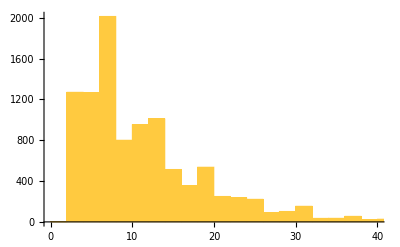

```mathematica
Histogram[Table[Prime[n+1]-Prime[n],{n,10000}]]
```

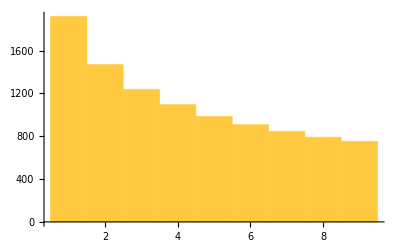

```mathematica
Histogram[Table[Part[IntegerDigits[n^2],1],{n,10000}]]
```

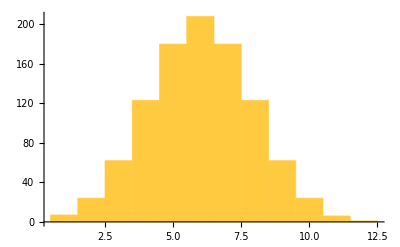

```mathematica
Histogram[Table[StringLength[RomanNumeral[n]],{n,1000}]]
```

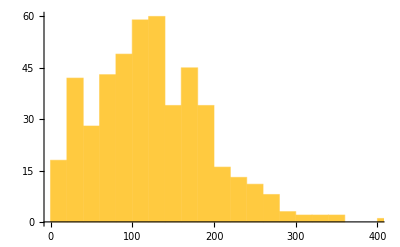

```mathematica
Histogram[StringLength[TextSentences[WikipediaData["computers"]]]]
```

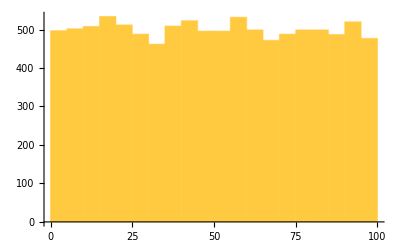
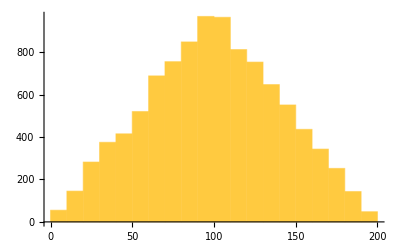
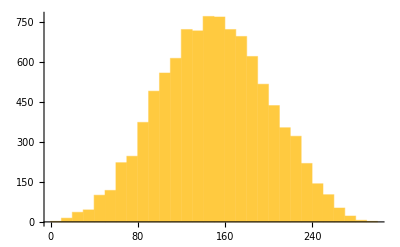
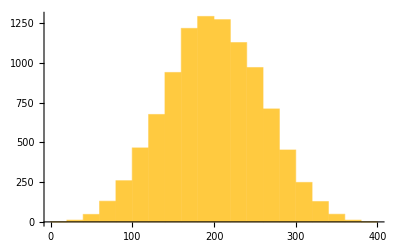
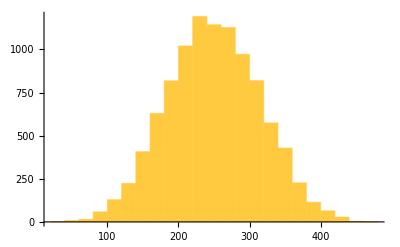

```mathematica
Table[Histogram[Table[Total[RandomReal[100,n]],10000]],{n,1,5}]
```

```mathematica
ListPlot3D[ImageData[Binarize[Graphics[Style[Text["W"],200]]]]]
```

-Graphics3D-

### Exercises from EIWL3 Section 25

```mathematica
f/@Range[5]
```

{f[1],f[2],f[3],f[4],f[5]}

```mathematica
f/@g/@Range[10]
```

{f[g[1]],f[g[2]],f[g[3]],f[g[4]],f[g[5]],f[g[6]],f[g[7]],f[g[8]],f[g[9]],f[g[10]]}

```mathematica
x//d//c//b//a
```

a[b[c[d[x]]]]

```mathematica
Alphabet[]//Framed
```

{a,b,c,d,e,f,g,h,i,j,k,l,m,n,o,p,q,r,s,t,u,v,w,x,y,z}

```mathematica
EntityValue[EntityClass["Planet",All],"Image"]//ColorNegate
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
GeoGraphics/@EntityList[EntityClass["Country","GroupOf5"]]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
ImageCollage[Binarize/@EntityClass["Country","Europe"][EntityProperty["Country","Flag"]]]
```

-Graphics-

```mathematica
Column[Map[DominantColors,EntityClass["Planet",All][EntityProperty["Planet","Image"]]]]
```

{GrayLevel[0.0003583326349482438],GrayLevel[0.5809817026568795],GrayLevel[0.2568999517211182]}
{RGBColor[0.8853258435338224, 0.6847277936008838, 0.4256700400270567],RGBColor[0.000642064098966206, 0.0014037306334321756, 0.000741076745930836]}
{RGBColor[0.0024606914773152946, 0.0024097879200276097, 0.0039673926952988985],RGBColor[0.38137481545229607, 0.40751891622899705, 0.48787187010084493],RGBColor[0.709369586353396, 0.7271479029748487, 0.8068003802783188],RGBColor[0.9792341683643001, 0.9822919853218711, 0.9938424909149209],RGBColor[0.6354966448798469, 0.547993401540665, 0.5436090454839879]}
{RGBColor[0.0012177112422530026, 0.0015444400900931803, 0.002282633031318643],RGBColor[0.5556976430545663, 0.4531266040635173, 0.3330454215920823],RGBColor[0.9766143421803483, 0.6748004340563882, 0.36945365634477967],RGBColor[0.2479853695341303, 0.28139542539507234, 0.26899239922440077],RGBColor[0.49662186211636067, 0.5143298694495971, 0.5023898427059187],RGBColor[0.6400489109534753, 0.7400325106312161, 0.8829327113481882]}
{RGBColor[0.0007307443638727919, 0.0007454981889383991, 0.0016562190320313643],RGBColor[0.6782699732325107, 0.6320729750699731, 0.5998391370238426],RGBColor[0.8542680796980542, 0.708030218110517, 0.5495188353805759],RGBColor[0.5603508590091927, 0.4463794024248931, 0.3598178308880452]}
{RGBColor[0.0008759690380522743, 0.000616761123413929, 0.0013660526470624804],RGBColor[0.3645501164755359, 0.3474409021418892, 0.3008581988199233],RGBColor[0.6925168887922426, 0.608767018411482, 0.4578034667819321],RGBColor[0.9019996092281926, 0.7638467049048333, 0.4927253941562712]}
{RGBColor[0.5487856264665472, 0.615474780101897, 0.6457820763462186],RGBColor[0.002625174628613325, 0.002077245768923338, 0.002466785942829536],RGBColor[0.2274835700706535, 0.24605670217787023, 0.25518636783414006]}
{RGBColor[0.6462468665348049, 0.7691692320553201, 0.8252791047389375],RGBColor[0.000144847552980187, 0.0001932677115112477, 0.0002527662080724566],RGBColor[0.4284148917082447, 0.5053577871902002, 0.5435623697797396]}

```mathematica
Total[LetterNumber["wolfram"]]
```

88